## 5

```mathematica
Integrate[1/(8 Pi)Exp[-r],{r,Infinity,0}]
%//N
```

-1/(8 π)

-0.0397887

```mathematica
N[-1/(8 π)/Integrate[1/(8 Pi)Exp[-r],{r,100,0}] -1,10]
```

3.720075976×10^-44

```mathematica
∫_∞^0 (∫-Exp[-r]/(8 π)ⅆr)ⅆr
%//N
```

-1/(8 π)

-0.0397887

### Substitution

```mathematica
D[x/(x-1)^2,x]//Simplify
```

-(1+x)/(-1+x)^3

```mathematica
Integrate[(1+x)/(x-1)^3 1/(8 Pi)Exp[-x/(x-1)^2],{x,0,1}]
%//N
```

-1/(8 π)

-0.0397887

```mathematica
Limit[x/(x-1)^2,{x->1}]
```

∞

```mathematica
Integrate[(1+x)/(x-1)^3 1/(8 Pi)Exp[-x/(x-1)^2],{x,0,a}]
```

ConditionalExpression[(-1+ⅇ^(-a/(-1+a)^2))/(8 π), Re[a]≤1||a∉ℝ]

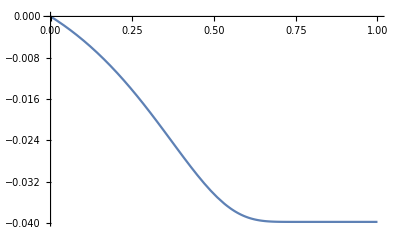

```mathematica
Plot[(-1+ⅇ^(-a/(-1+a)^2))/(8 π),{a,0,1}]
```

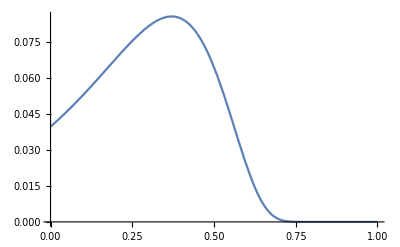

```mathematica
Plot[-(1+x)/(x-1)^3 1/(8 Pi)Exp[-x/(x-1)^2],{x,0,1},PlotRange->All]
```

120208

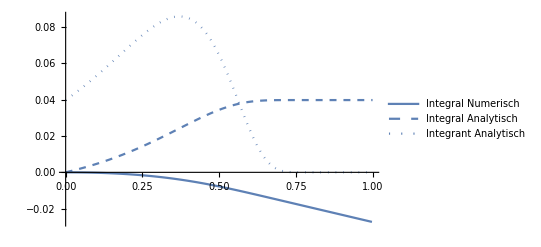

```mathematica
SetDirectory[NotebookDirectory[]];
PrintTemporary["plot"];
d= Import["poisson2.dat"];
ByteCount[d]

Show[
{
ListLinePlot[{d[[All,{1,2}]]},PlotLegends->{"Integral Numerisch", "ρ"}],
Plot[-(-1+ⅇ^(-a/(-1+a)^2))/(8 π),{a,0,1},PlotStyle->Dashed,PlotLegends->{"Integral Analytisch"}],
Plot[-(1+x)/(x-1)^3 1/(8 Pi)Exp[-x/(x-1)^2],{x,0,1},PlotStyle->Dotted,
PlotLegends->{"Integrant Analytisch"}]
},
PlotRange->All
]

Export["img/poisson2.pdf",%];
```

96192

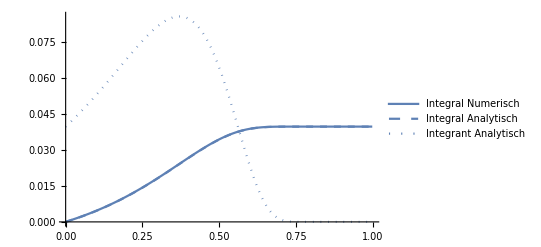

```mathematica
SetDirectory[NotebookDirectory[]];
d= Import["summation.dat"];
ByteCount[d]

Show[
{
ListLinePlot[{d[[All,{1,2}]]},PlotLegends->{"Integral Numerisch", "ρ"}],
Plot[-(-1+ⅇ^(-a/(-1+a)^2))/(8 π),{a,0,1},PlotStyle->Dashed,PlotLegends->{"Integral Analytisch"}],
Plot[-(1+x)/(x-1)^3 1/(8 Pi)Exp[-x/(x-1)^2],{x,0,1},PlotStyle->Dotted,
PlotLegends->{"Integrant Analytisch"}]
},
PlotRange->All
]

Export["img/summation.pdf",%];
```

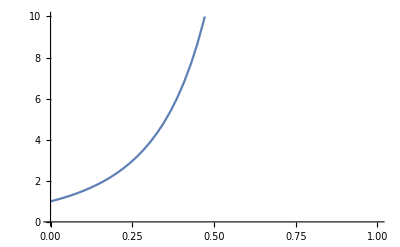

```mathematica
Plot[-(1+x)/(x-1)^3,{x,0,1},PlotRange->{0,10}]
```

## 2. Aufgabe

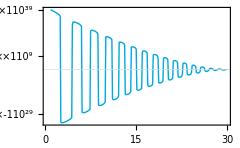

```mathematica
SetDirectory[NotebookDirectory[]];

d=Import["errorFkt.dat"];
ListLinePlot[d[[10;;-1]],
ScalingFunctions->"SignedLog",PlotRange->All,
FrameLabel->{"E","F(E)"},
Axes->False,
GridLines->{None,{0}},GridLinesStyle->Automatic
]
Export["img/errorFunction.pdf",%];
```

724240

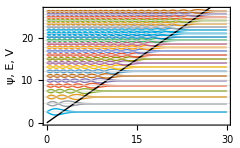

```mathematica
SetDirectory[NotebookDirectory[]];
d=Import/@FileNames["out*.dat"];
e = d[[All,1,1]];
d=d[[All,2;;-1]];
dInv = d;
dShow = d;
dInv[[All,All,2]]*=-1;
dShow[[All,All,2]]=d[[#,All,2]]+e[[#]]&/@Range@Length@d;
dInv[[All,All,2]]=dInv[[#,All,2]]+e[[#]]&/@Range@Length@d;
ByteCount[d]

Show[
ListLinePlot[
dShow,
GridLines->{None,e},
GridLinesStyle->Automatic,
FrameTicks->{{Automatic,e},Automatic},
FrameLabel->{"x","ψ, E, V"}
],
ListLinePlot[dInv],
Plot[x,{x,0,100},PlotStyle->Directive[Black]]
]
(*Export["img/out.pdf",%];*)
```

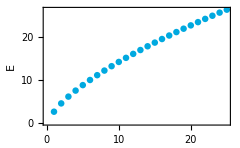

```mathematica
Show[
ListPlot[e,
FrameLabel->{"n","E"}
]
]
(*Export["img/trend.pdf",%];*)
```

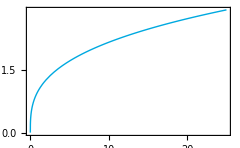

```mathematica
Plot[x^(1/3),{x,0,25}]
```

```mathematica
mdl/@Range[20]
```

{3.86426,4.97174,6.07922,7.1867,8.29418,9.40166,10.5091,11.6166,12.7241,13.8316,14.9391,16.0465,17.154,18.2615,19.369,20.4765,21.5839,22.6914,23.7989,24.9064}

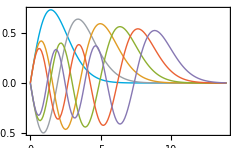

```mathematica
ListLinePlot[d]
```